# Vaje za 5. teden

20. 3. 2025

## Naloga 1

Napiši funkcijo odvodPolinoma, ki kot argument sprejme polinom v splošni obliki in vrne njegov odvod. Pri tem uporabi le prepisovalna pravila. S pomočjo te funkcije odvajaj polinom x^2 + 3x + 4.

```mathematica
prep :=  {x^a_ -> a*x^(a- 1), x-> 1 } ;
```

```mathematica
OdvodPolinoma[p_] := (p /. prep) - (p /. {x -> 0})
```

```mathematica
OdvodPolinoma[x^2 + 3x + 4]
```

3+2 x

SetDelayed::write: Tag Slot in #1[x_] is Protected.

$Failed

## Naloga 2 - rešite 3. kolokvij iz matematike

-Graphics-

```mathematica
f[x_] := Piecewise[{
{ArcTan[1/(x^2-1)], x > 1},
{a, x==1},
{Divide[b Sin[x-1], x^2 -1], x<1}
}]
limita1 = Limit[f[x], {x->1}, Direction->"FromAbove"]
limita2 = Limit[f[x], {x->1}, Direction->"FromBelow"]
Solve[limita1 ==a==limita2]
```

π/2

b/2

{{a→π/2,b→π}}

-Graphics-

{1,√2}

x/(√(1+x^2))

1/(√2)

-√2

{{n→2 √2}}

2 √2-√2 y

{1/2 (√2-√2 √(1-4 √2+2 a)),1/2 (√2+√2 √(1-4 √2+2 a))}

{a→-1/2+2 √2}

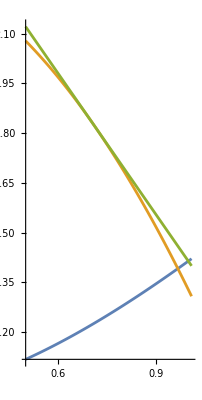

```mathematica
f[x_] := Sqrt[x^2 + 1]
T = {1, f[1]}
df = D[f[x], x]
kTangente = df /. {x -> 1}
kNormale = -1/kTangente
g[x_] := a - x^2
Solve[Sqrt[2] == kNormale * 1 + n]
Normala[x_] := kNormale*x + 2 Sqrt[2]
Normala[y]
presecisca = Solve[Normala[x] == g[x], {x}] //Values // Flatten
resitev = Solve[presecisca[[1]] == presecisca[[2]]] //FullSimplify  //Flatten

G[x_] := g[x] /. resitev
Plot[{f[x], G[x], Normala[x]}, {x, 0.5, 1.01}, AspectRatio-> Automatic]
```

-Graphics-

-Graphics-

## Naloga 3

Funkcija f je podana s predpisom f(x) = ln((x^2-1)/2x). Določite definicijsko območje funkcije in ugotovite če je injektivna.

## Naloga 4

Izračunajte integral funkcije f(x, r) = ArcTan(r x) / (x (1 + x^2)) po spremenljivki x v odvisnosti od parametra r, kjer gre integral od nič do neskončno. Dobljeno preslikavo tudi poenostavite in narišite.

## Naloga 5

Izračunajte naslednje neskončne vsote 
a) 1 + 1 / 2 + 1 / 3 + 1 / 4 + ...  
b) 1 - 1 / 2 + 1 / 3 - 1 / 4 + ...
c) 1 + 1/ 4 + 1 / 9 + 1 / 16 + 1 / 25 + ...

## Naloga 6

Izračunajte posplošena integrala naslednjih funkcij
a) f(x) = ln(x) / (1 - x) na mejah od 0 do 1,
b) f(x) = sin(x) / x na mejah od nič do neskončno,
c) f(x) = 1 / x^(1/2) na mejah od 0 do 1
Ali za izračun potrebujete ukaz Limit?